# Project

Facial images convey many important human characteristics, such as identity, gender, expression, age, and ethnicity. 
Representative examples including face recognition, facial expression recognition, age estimation, gender classification and ethnicity recognition.

The database includes around 50% Caucasians, 40% Asians, 7% African Americans, and 3% others; 40% of the 150 images are father-son pairs, 22% are father-daughter, 13% are mother-son, and 26% are mother-daughter. Therefore, it has a wide spread distribution of facial characteristics which depend on race, gender, age, career, etc. 

Objective:
Identify the kinship using faces.

Dataset:
- Labeled faces in the Wild

```mathematica
FeatureExtraction
```

```mathematica
MorphologicalPerimeter
```

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son"]
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/father-son

```mathematica
ClearAll[dataFatherSon];
```

```mathematica
fatherSon=Import["fs*"];
```

```mathematica
createCouples[ imgs_List ] := Partition[ imgs , 2 ] ;

fakeCouples[ imgs_List ] := Transpose[
								{RandomSample[Transpose[createCouples[imgs]][[1]]] , RandomSample[Transpose[createCouples[imgs]][[2]]]}];
                                       
                                          
                                                                 
createClasses[ imgs_List,{ n_Integer, m_Integer },{ j_Integer, k_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> "couples" ,
                                     #2 -> "fake couples"
                                    } & ,
                                    
                                   { createCouples[Take[
                                           imgs ,
                                          {n, m}
                                          ]],
                                      fakeCouples[ Take[ imgs, {j,k}]]
                                   }
                                 ]
                               ];

 createClassesNeural[ imgs_List,{ n_Integer, m_Integer },{ j_Integer, k_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> 1 ,
                                     #2 -> 2
                                    } & ,
                                    
                                   { createCouples[Take[
                                           imgs ,
                                          {n, m}
                                          ]],
                                      fakeCouples[ Take[ imgs, {j,k}]]
                                   }
                                 ]
                               ];
```

```mathematica
fakeCouples[Take[fatherSon,{1,10}]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
trainingSet = createClasses[fatherSon,{11,110}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
trainingSet = createClasses[fatherSon,{1,100},{101,200}]
```

{{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples,{-Graphics-,-Graphics-}→couples,{-Graphics-,-Graphics-}→fake couples}

```mathematica
validationSet = createClasses[fatherSon,{401,450},{451,500}];
```

```mathematica
testSet = createClasses[fatherSon,{201,300},{301,400}];
```

```mathematica
cl=Classify[
trainingSet, 
ValidationSet-> validationSet
 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,testSet]
```

ClassifierMeasurementsObject[…]

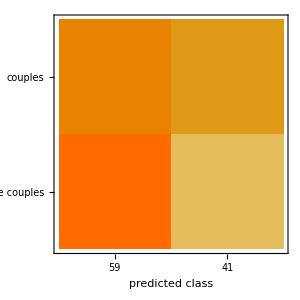

```mathematica
%["ConfusionMatrixPlot"]
```

## Dataset 1

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-I/images/father-son"];
ClearAll[fatherSonDS1];
fatherSonDS1=Import["fs*"];
Length[fatherSonDS1]
```

312

```mathematica
trainingSet = createClasses[fatherSonDS1,{1,62},{63,124}];
```

```mathematica
validationSet = createClasses[fatherSonDS1,{249,280},{281,312}];
```

```mathematica
testSet = createClasses[fatherSonDS1,{125,186},{187,248}];
```

```mathematica
cl=Classify[
trainingSet, 
ValidationSet-> validationSet
 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[cl,testSet]
```

ClassifierMeasurementsObject[…]

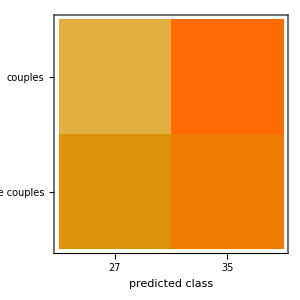

```mathematica
%["ConfusionMatrixPlot"]
```

# Feature extraction approach

## Neural network approach

```mathematica
convP = Take[NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"], {1, "4b22"}];
```

```mathematica
fmodel2 = NetGraph[{convP, convP, CatenateLayer[], FlattenLayer[], LinearLayer[128], Ramp, LinearLayer[], SoftmaxLayer[]}, {NetPort["Parent"]->1->3, NetPort["Child"]->2->3, 3->4, 4->5, 5->6, 6->7->8}, "Output"->NetDecoder[{"Class",{"Parent","Not related"}}]];
```

```mathematica
Length[fatherSon]
```

500

```mathematica
dataFatherSon=AssociationThread[{"Parent","Child"}-> Transpose@Partition[fatherSon, 2]];
realFatherSon=AssociationThread[{"Parent","Child","Output"}-> {Transpose[Partition[Take[fatherSon,200], 2]][[1]],Transpose[Partition[Take[fatherSon,200], 2]][[2]],Table["Parent",200]}];
fakeFatherSon=AssociationThread[{"Parent","Child","Output"}->{RandomSample[Transpose[Partition[Take[fatherSon,{201,400}], 2]][[1]]],RandomSample[Transpose[Partition[Take[fatherSon,{201,400}], 2]][[2]]],Table["Not related",200]}];
```

```mathematica
Keys[<|"Parent"->{1,2},"Child"->{A,B},"Output"->{1,2}|>]
```

{Parent,Child,Output}

```mathematica
MapIndexed[First[{"Parent","Child","Output"}[[#2]]]->Flatten[#1] &,
Transpose[{Values[<|"Parent"->{1,2},"Child"->{A,B},"Output"->{1,2}|>],Values[<|"Parent"->{3,4},"Child"->{c,d},"Output"->{3,4}|>]}]]
```

{Parent→{1,2,3,4},Child→{A,B,c,d},Output→{1,2,3,4}}

```mathematica
FlattenAt[Transpose[{Values[<|"Parent"->{1,2},"Child"->{A,B},"Output"->{1,2}|>],Values[<|"Parent"->{3,4},"Child"->{c,d},"Output"->{3,4}|>]}],-1]
```

{{{1,2},{3,4}},{{A,B},{c,d}},{1,2},{3,4}}

```mathematica
MapThread[,
List[Values[<|"Parent"->{1,2},"Child"->{A,B},"Output"->{1,2}|>],Values[<|"Parent"->{3,4},"Child"->{c,d},"Output"->{3,4}|>]]]
```

{{{1,2},{A,B},{1,2}},{{3,4},{c,d},{3,4}}}

```mathematica
AssociateTo[<|"Parent"->{1,2},"Child"->{A,B},"Output"->{1,2}|>,<|"Parent"->{3,4},"Child"->{c,d},"Output"->{3,4}|>]
```

<|Parent→{3,4},Child→{c,d},Output→{3,4}|>

```mathematica
realFatherSon
```

<|Parent→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Child→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Output→{Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent,Parent}|>

```mathematica
net = NetInitialize[fmodel2]
```

```mathematica
data
```

Take[<|Parent→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Child→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>,10]

```mathematica
model = NetTrain[net,data , LearningRateMultipliers->{"1"->None, "2"-> None, _->1}]
```

NetGraph[<>]

```mathematica
model[testSet]
```

{Parent}

```mathematica
testSet=<|"Parent"->{ -Graphics-},"Child"->{-Graphics-},"Output"-> "Parent"|>
```

<|Parent→{-Graphics-},Child→{-Graphics-},Output→Parent|>

```mathematica
testSet
```

<|Parent→{-Graphics-},Child→{-Graphics-},Output→Parent|>

```mathematica
ClassifierMeasurements[model,testSet,"Accuracy"]
```

ClassifierMeasurements::mlbftlgth2: Example … should have 2 features instead of 0.

Proposal 1
Binary classification

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images

Partition::pdep: Depth 1 requested in object with dimensions {}.

MapThread::mptd: Object Partition[fatherDaughter,2] at position {2, 1} in MapThread[{#1→FatherDaughter}&,{Partition[fatherDaughter,2]}] has only 0 of required 1 dimensions.

```mathematica
SetDirectory["/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images/"]
fatherSon=Import["father-son/fs*"];
dataFatherSon=Flatten@MapThread[{#->"FatherSon"}&,{Partition[fatherSon,2]}];

fatherDaugther=Import["father-dau/fd*"];
dataFatherDaugther=Flatten@MapThread[{#->"FatherDaughter"}&,{Partition[fatherDaughter,2]}];
```

/Users/Said/Github/Said_Summer2018/Data/KinFaceW-II/images

Partition::pdep: Depth 1 requested in object with dimensions {}.

MapThread::mptd: Object Partition[fatherDaughter,2] at position {2, 1} in MapThread[{#1→FatherDaughter}&,{Partition[fatherDaughter,2]}] has only 0 of required 1 dimensions.

```mathematica
Manipulate[ImageAssemble[ImageResize[#,{100,100}]&/@ dataFatherSon⟦i⟧],{i,1,Length[dataFatherSon],1}]
```

```mathematica
averageColor[img_] := Total[Flatten[ImageData[img],1],{1}] / 
(Times @@ ImageDimensions[img])
```

```mathematica
FeatureExtraction[dataFatherSon[[1]][[1]]]
```

FeatureExtraction::mlmpty: The dataset should contain at least one example.

```mathematica
FacialFeatures[dataFatherSon[[1]][[1]],"NosePoints"]
```

{}

```mathematica
dataFatherSon[[1]][[1]]
```

```mathematica
FacialFeatures[dataFatherSon[[5]]]
```

{{},{<|Image→-Graphics-,Age→30,Gender→Female,Emotion→sadness|>}}

# Vectors ResNet

```mathematica
features=NetModel["ResNet-101 Trained on Augmented CASIA-WebFace Data"][fatherSon];
```

```mathematica
features[[1]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Said/Github/Said_Summer2018/Project

```mathematica
Export["processedImagesResNet_101.mx",features,"MX"]
```

processedImagesResNet_101.mx

```mathematica
Export["images_classes_validationset.mx",validationSet,"MX"];
Export["images_classes_trainingset.mx",trainingSet,"MX"];
Export["images_classes_testset.mx",testSet,"MX"];
```

```mathematica
f=Import["processedImagesResNet_101.mx"];
```

```mathematica
f[[1]]
```

```mathematica
Map[RotateLeft[ # , 1 ]&,Partition[RotateLeft[ {1,2,3,4} , 1 ],2]]
```

{{3,2},{1,4}}

```mathematica
createCouples[
                                          RotateLeft[ imgs , 1 ]
                                         ]
```

```mathematica
createCouples[ imgs_List ] := Partition[ imgs , 2 ] ;

fakeCouples[ imgs_List ] := Map[
                                 RotateLeft[ # , 1 ] & ,
                                 Partition[RotateLeft[ imgs , 1 ] , 2 ]
                                 
                                ];

                                                       
createClasses[ imgs_List, { n_Integer, m_Integer }] := 
                         Flatten[
                                 MapThread[
                                 
                                   { #1 -> "couples" ,
                                     #2 -> "fake couples"
                                    } & ,
                                    
                                   { Take[
                                          createCouples[ imgs ],
                                          {n, m}
                                          ],
                                     Take[
                                          fakeCouples[ imgs ],
                                          {n, m}
                                          ]
                                   }
                                 ]
                               ];
```

```mathematica
f//Length
```

500

```mathematica
createClasses[f,{1,200}]
```

```mathematica
trainingSet = createClasses[f,{1,100}];
```

```mathematica
validationSet = createClasses[f,{101,150}];
```

```mathematica
testSet = createClasses[f,{151,200}];
```

couples

```mathematica
clvectores=Classify[
trainingSet, 
ValidationSet-> validationSet

 ]
```

ClassifierFunction[…]

```mathematica
ClassifierMeasurements[clvectores,testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
createClasses[f]
```

createClasses[{{0.036862,0.0338027,0.250632,0.,0.,0.0532649,0.655749,2.52846,0.941102,0.0670733,0.593426,2.68666,0.,5.56874,0.0382102,1.11091,2016,0.159244,0.000385965,0.,3.09961,0.237749,0.,3.23726,0.,0.000413366,4.14144,0.222531,1.08564,0.275688,3.93431,0.0109102,2.70382},498,{1}}]
 |  |  |  |

```mathematica
fa
```

```mathematica
points=DimensionReduce[features,2,Method-> "TSNE"]
```

```mathematica
Dimensions[points]
```

{500,2}

```mathematica
Graphics[MapThread[Inset[#1,#2,{0,0},0.5]&, {fatherSon,points}], ImageSize->Full, ImagePadding->25]
```

-Graphics-

```mathematica
FeatureNearest[fatherSon, -Graphics-, 5, 
 FeatureExtractor -> 
  NetModel["ResNet-101 Trained on Augmented Casia WebFace Data"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}